# Seminarska naloga

## Obdelava statističnih podatkov

Liam Mislej

Fakulteta za matematiko in fiziko

13.2.2019

## Primerjava BDP Slovenije z mejnimi državami

### Mejne države

V spodnjem prikazu vidimo sosednje države slovenije, ki so povezane z črtami. Dvojne črte pomenijo to , da dve sosednji državi skupaj mejita še na tretjo državo, ali drugače povedano, nastopi tromeja.

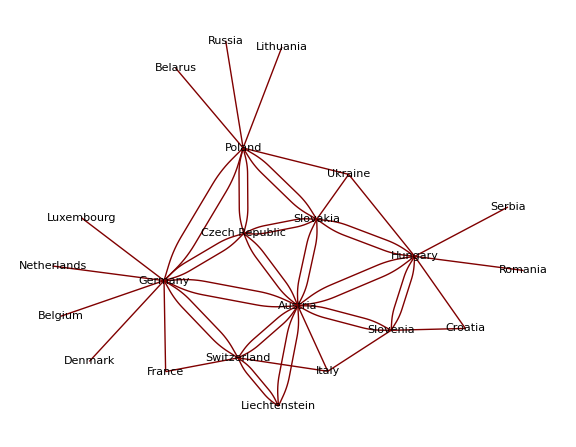

```mathematica
GraphPlot[Flatten[Thread[#->CountryData[#,"BorderingCountries"]]&/@CountryData["CentralEurope"]],VertexLabeling->True,ImageSize->Large]
```

### Bdp na prebivalca

V spodnjem delu sem primerjal BDP na prebivalca slovenije z mejnimi državami ter tudi naravni prirastek.

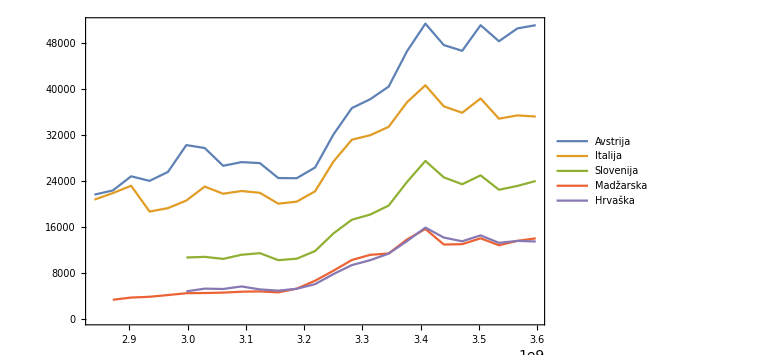

```mathematica
slo = CountryData["Slovenia",{{"GDPPerCapita"},{1990,2015}}];
aus = CountryData["Austria",{{"GDPPerCapita"},{1990,2015}}];
ita = CountryData["Italy",{{"GDPPerCapita"},{1990,2015}}];
cro = CountryData["Croatia",{{"GDPPerCapita"},{1990,2015}}];
mad = CountryData["Hungary",{{"GDPPerCapita"},{1990,2015}}];
svet = CountryData["World",{{"GDPPerCapita"},{1990,2015}}];
DateListPlot[{aus,ita,slo,mad,cro,svet},{1990,2015},PlotLegends->{"Avstrija","Italija","Slovenija","Madžarska","Hrvaška"},ImageSize->Large]
```

V zgornjem grafu se lepo vidi vpliv svetovne gospodarske krize, ki je začela leta 2008. Opazimo padec pri vseh državah.

### Naravni prirastek

V spodnjem grafu so prikazani naravni prirastki populacije podanih držav.

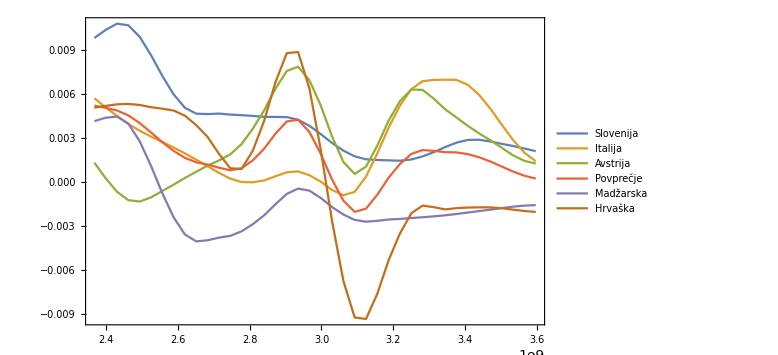

```mathematica
slo = CountryData["Slovenia",{{"PopulationGrowth"},{1975,2015}}];
aus = CountryData["Austria",{{"PopulationGrowth"},{1975,2015}}];
ita = CountryData["Italy",{{"PopulationGrowth"},{1975,2015}}];
cro = CountryData["Croatia",{{"PopulationGrowth"},{1975,2015}}];
mad = CountryData["Hungary",{{"PopulationGrowth"},{1975,2015}}];
povprecno = (slo +aus +ita+cro +mad )/5;
DateListPlot[{slo,ita,aus,povprecno,mad,cro},{1975,2015},PlotLegends->{"Slovenija","Italija","Avstrija","Povprečje","Madžarska","Hrvaška"},ImageSize->Large]
```

## BDP znotraj Slovenije

### BDP po regijah

Še nekaj podatkov znotraj slovenije. Podatke sem pridobil iz spletne strani SloStat, jih shranil v excel ter importal v mathematico.

```mathematica
SetDirectory[NotebookDirectory[]];
podatki = Import["gdpprebregije.xlsx"]//First;
```

```mathematica
podatki//TableForm
```

Pomurska | Podravska | Koroška | Savinjska | Zasavska | Posavska | Jugovzhodna Slovenija | Osrednjeslovenska | Gorenjska | Primorsko-notranjska | Goriška | Obalno-kraška
7813. | 9134. | 9365. | 10005. | 8171. | 9295. | 10878. | 15540. | 9840. | 8970. | 10812. | 11822.
8185. | 9638. | 9984. | 10380. | 8323. | 9732. | 11325. | 16563. | 10490. | 9142. | 11407. | 12391.
8651. | 10457. | 10253. | 11257. | 8387. | 10618. | 12139. | 17720. | 11166. | 9709. | 12161. | 13305.
8862. | 10780. | 10498. | 11674. | 8437. | 10449. | 12657. | 19250. | 11637. | 9954. | 12565. | 13964.
9399. | 11427. | 10945. | 12306. | 8792. | 10994. | 13527. | 20255. | 12306. | 10383. | 13054. | 14661.
9713. | 12021. | 11600. | 13013. | 9309. | 11812. | 13956. | 21403. | 12706. | 10680. | 13692. | 15271.
10220. | 13028. | 12196. | 13758. | 9715. | 12466. | 15343. | 23255. | 13419. | 11396. | 14592. | 16542.
11164. | 14521. | 13434. | 15219. | 10552. | 13809. | 16874. | 25668. | 14874. | 12588. | 16511. | 18391.
11893. | 15724. | 14388. | 16799. | 11382. | 15025. | 18138. | 27227. | 15858. | 13579. | 17907. | 20102.
11413. | 14745. | 13130. | 15717. | 10700. | 14432. | 16772. | 26020. | 14346. | 12895. | 16684. | 19147.
11366. | 14606. | 13131. | 16033. | 10795. | 14432. | 16841. | 25709. | 14646. | 12471. | 16559. | 19226.
11866. | 14915. | 13773. | 16501. | 10867. | 14906. | 17048. | 25923. | 14906. | 12555. | 16568. | 19068.
11771. | 14537. | 13816. | 16122. | 10312. | 14597. | 16467. | 25439. | 14610. | 12080. | 15988. | 17777.
12045. | 14571. | 14027. | 16113. | 10397. | 14830. | 16715. | 25230. | 15107. | 12423. | 15962. | 17299.
12476. | 15194. | 14617. | 16653. | 10337. | 15354. | 17539. | 25890. | 15990. | 13124. | 16525. | 17764.
12636. | 15602. | 15220. | 17327. | 10186. | 15775. | 18158. | 26580. | 16522. | 13912. | 17260. | 18859.
13217. | 16037. | 15776. | 18029. | 10469. | 16161. | 18544. | 27576. | 17255. | 14418. | 17980. | 19896.
13978. | 16840. | 16561. | 19045. | 10910. | 17326. | 20467. | 29371. | 18507. | 15005. | 19131. | 21242.

```mathematica
Imena[podatki_]:=First[podatki];
Bdp[podatki_]:=Rest[podatki];
IndeksStolpca[podatki_, stolpec_] := Module[{res},
res =Position[Imena[podatki], stolpec];
If[Length[res] == 0, Null, res[[1,1]]]
];
Stolpec[podatki_, stolpec_] := Bdp[podatki] // 
							Transpose // 
							(#[[IndeksStolpca[podatki, stolpec]]])&
```

```mathematica
pomurska = Stolpec[podatki,"Pomurska"];
podravska = Stolpec[podatki,"Podravska"];
koroška= Stolpec[podatki,"Koroška"];
savinjska = Stolpec[podatki,"Savinjska"];
zasavska= Stolpec[podatki,"Zasavska"];
posavska = Stolpec[podatki,"Posavska"];
jugovzhodnaslovenija = Stolpec[podatki,"Jugovzhodna Slovenija"];
osrednjeslovenska = Stolpec[podatki,"Osrednjeslovenska"];
gorenjska = Stolpec[podatki,"Gorenjska"];
primorskonotranjska = Stolpec[podatki,"Primorsko-notranjska"];
goriška = Stolpec[podatki,"Goriška"];
obalnokraška = Stolpec[podatki,"Obalno-kraška"];
ListLinePlot[{pomurska,podravska,koroška,savinjska,zasavska,posavska,jugovzhodnaslovenija,osrednjeslovenska,gorenjska,primorskonotranjska,goriška,obalnokraška,svetovnopovp},PlotLabels->Placed[{"Pomurska","Podravska","Koroška","Savinjska","Zasavska","Posavska","Jugo-Vzhodna Slovenija","Osrednje-Slovenska","Gorenjska","Primorsko-Notranjska","Goriška","Obalno-Kraška","Svetovno Povprečje"}],ImageSize->Large]
```

-Graphics-

### Primerjava z svetovnim povprečjem

Primerjava svetovnega BDP-ja z slovenskim od leta 2000 do 2017.

```mathematica
svetovnopovp = {7935.,8212.,8498.,8862.,9463.,10084.,10909.,11676.,12213.,12181.,12839.,13559.,14108.,14698.,15264.,15718.,16247.,16952.};
slogdp = Import["SloGdpPoPreb1.xlsx"]//First;
slogdp1 = Stolpec[slogdp,"Slovensko povprečje"];
podatki2 = {};
Append[podatki2,slogdp1];
Append[podatki2,svetovnopovp];
ListLinePlot[{slogdp1,svetovnopovp},PlotLabels->Placed[{"Slovensko povprečje","Svetovno povprečje"}],ImageSize->Large,
PlotLabel -> "Od leta 2000 naprej"]
```

-Graphics-

## Število prebivalcev po starosti

### Primerjava leta 2000 in 20018

```mathematica
starost =First[First[Import["PoStarosti2000.xlsx"]]];
postarosti2 = Part[First[Import["PoStarosti2018.xlsx"]],2];
postarosti1 = Part[First[Import["PoStarosti2000.xlsx"]],2];
PairedBarChart[{postarosti1},{postarosti2},ChartLabels->starost,ImageSize->Large,ChartStyle->{{Red,Blue},None,None},ChartLegends->{{"Leto 2000","Leto 2018"},None,None}]
```

-Graphics-

### Nekaj podatkov

Povprečna starost

```mathematica
starost2 = {4,9,14,19,24,29,34,39,44,49,54,59,64,69,74,79,84,89,94,99};
povprecnastarost[leta_,stpoletih_]:= Total[(leta * stpoletih)]/Total[stpoletih];
```

```mathematica
povpstarost2000 = povprecnastarost[starost2,postarosti1]
```

40.2879

```mathematica
povpstarost2018 = povprecnastarost[starost2,postarosti2]
```

44.8154

```mathematica
stevilopreb[stpoletih_]:=Total[stpoletih];
```

```mathematica
stpreb2000 = stevilopreb[postarosti1]
```

1.99021×10^6

```mathematica
stpreb2018 = stevilopreb[postarosti2]
```

2.06988×10^6

Prirastek od leta 2000 do 2018

```mathematica
prirastek = stpreb2018 - stpreb2000
```

79664.